# NV-center qubits

## Connectivity : star Main ref: Abobeih

Set environment, such as threads, gpu, etc.

```mathematica
(*SetEnvironment["OMP_NUM_THREADS"->"8"]*)
SetDirectory[NotebookDirectory[]];
```

Load the QuESTLink

```mathematica
Import["/home/cica/programs/QuESTlink/Link/QuESTlink.m"];
CreateLocalQuESTEnv["quest_link_gpu"];
```

NV-center device, loaded after questlink

```mathematica
Get["../vqd.wl"];
```

## User device configuration

Qubit 0 indicates electron spin,and the rest are nuclear spins  C^13 and N^14 - if applicable
Time unit is second
Frequency unit is  Hertz
Each qubit has unique characteristics

```mathematica
Options[NVCenterDelft]={
qubitsNum->6,
T1-> <|0-> 3600,1->60,2->60,3->60,4->60,5->60 |>,
(* we assume T2* echoed out to T2*)
T2-> <|0-> 1.5,1->10,2->10,3->10,4->9,5->9|>,

(** Global magnetic field fluctuation due to^13 C bath 
Causes dephasing on the electron in 4 μs
External field is effectively perfect
**)
GlobalField-><|#->RandomReal[{-0.01,0.01}]&/@Range[0,5]|>,
(* ??? *)
GlobalFieldDetuning->66000,

(* rates are Hz. Direct single rotation on Nuclear spin is done via RF, put electron in state -1 leave out the Rx Ry on nuclear spins?*)
FreqSingleXY-> <|0->15*10^6,1->500 ,2->500,3->500,4->500,5->500|>,
FreqSingleZ-><|0->32*10^6,1->400*10^3,2->400*10^3,3->400*10^3,4->400*10^3,5->400*10^3|>,

(* 2-qubit gates can be done via dynamical decoupling or dd+RF. The gate is conditioned on electron spin state *)
FreqCRot-> <|1-> 1.5*10^3,2->2.8*10^3,3->0.8*10^3,4->2*10^3 ,5->2*10^3|>,
(* approx 95-99 *)
FidCRot-><|1-> 0.98,2->0.98, 3->0.98,4->0.98 ,5->0.98|>,
(* fidelities are in percent and is obtained from random becnhmarking by default *)
FidSingleXY-> <| 0->0.9995,1-> 0.995,2->0.995, 3->0.99,4->0.99,5->0.99 |>,
FidSingleZ->  <| 0->0.9999,1-> 0.9999,2->0.99999, 3->0.9999,4->0.999,6->0.99 |>,
(** Error ratio {depolarizing error, dephasing ratio}, where the ratios are sum to one. characterizes inhomogenieties between depolarizing and dephasing noises **)
(* For single rotations *)
EFSingleXY->{0.75,0.25},
(* For conditional rotations CRx and CRy. Note that, applying single rotations on nuclear spins mean applying conditional rotations *)
EFCRot->{0.9,0.1},
(** Initialization and destructive measurement on the electron spin.
nuclear spin init and measurement are done on the electron-spin through swap sequence **)
FidInit-> 0.999,
DurInit->2*10^-3,
(** measurements **)
FidMeas->0.946,
(* 10-20 μs *)
DurMeas->2*10^-5
};
```

## Introduction to essential elements

```mathematica
nvnode=NVCenterDelft[];
```

The native gates:

```mathematica
nvnode[Gates]⟦All,1⟧//Column
```

Init_(VQD`Private`q$_)/;VQD`Private`q$===0
M_(VQD`Private`q$_)/;VQD`Private`q$===0
Wait_(VQD`Private`qubits$__)[VQD`Private`dur$_]
Rz_(VQD`Private`q$_)[VQD`Private`θ$_]
Rx_(VQD`Private`q$_)[VQD`Private`θ$_]/;VQD`Private`q$===0
Ry_(VQD`Private`q$_)[VQD`Private`θ$_]/;VQD`Private`q$===0
Rx_(VQD`Private`q$_)[VQD`Private`θ$_]/;VQD`Private`q$>0
Ry_(VQD`Private`q$_)[VQD`Private`θ$_]/;VQD`Private`q$>0
CRx_(VQD`Private`e$_,VQD`Private`n$_)[VQD`Private`θ$_]/;VQD`Private`e$==0&&VQD`Private`n$>0
CRy_(VQD`Private`e$_,VQD`Private`n$_)[VQD`Private`θ$_]/;VQD`Private`e$==0&&VQD`Private`n$>0

## Common gates on nuclear spins obtained by sequence of native gates

```mathematica
(* cotrolled-pauli gates, where control qubits are the electron spins *)
Subscript[cX, c_,t_]:=Sequence@@{Subscript[CRx, c,t][π/2],Subscript[Rz, c][-π/2],Subscript[Rx, t][-π/2]}
Subscript[cY, c_,t_]:=Sequence@@{Subscript[CRy, c,t][π/2],Subscript[Rz, c][-π/2],Subscript[Ry, t][-π/2]}
Subscript[cZ, c_,t_]:=Sequence@@{Subscript[Rx, t][π/2],Subscript[CRy, c,t][-π/2],Subscript[Rz, c][-π/2],Subscript[Ry, t][π/2],Subscript[Rx, t][-π/2]}
(* initialisation the nuclear spins *)
Subscript[initNcl, q_/;q>0]:=Sequence@@{Subscript[Ry, 0][π/2],Subscript[CRx, 0,q][π/2],Subscript[Rx, 0][π/2],Subscript[CRy, 0,q][-π/2],Subscript[Init, 0]}
(*measurement sequences on nuclear spins the computational basis *)
Subscript[measZ, q_/;q>0]:=Sequence@@{Subscript[Rx, 1][π/2],Subscript[Ry, 0][π/2],Subscript[CRy, 0,1][π/2],Subscript[Rx, 0][π/2],Subscript[M, 0]}
```

{Ry_0[π/2],CRx_(0,1)[π/2],Rx_0[π/2],CRy_(0,1)[-π/2],Init_0}

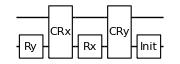

```mathematica
{Subscript[initNcl, 1]}
DrawCircuit@%
```

## 6 Qubits initialization

Initialize all qubits to zero

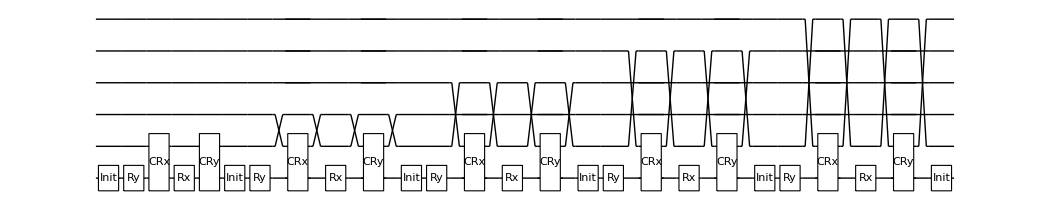

```mathematica
circInit={Subscript[Init, 0],Subscript[initNcl, 1],Subscript[initNcl, 2],Subscript[initNcl, 3],Subscript[initNcl, 4],Subscript[initNcl, 5]};
DrawCircuit[circInit]
```

```mathematica
ρ=CreateDensityQureg[6];
ρ2=CreateDensityQureg[6];
ψ=CreateQureg[6];
```

```mathematica
SetQuregMatrix[ρ,RandomMixState[6]];
CalcFidelity[ρ,InitZeroState@ψ]
```

0.0175169

Initialization on the noisy circuit. Serialize[circ] removes parallelism in the circuit.

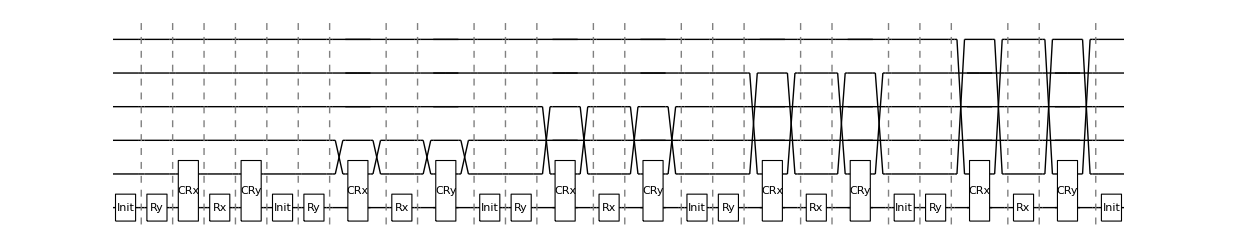

```mathematica
DrawCircuit@Serialize@circInit
```

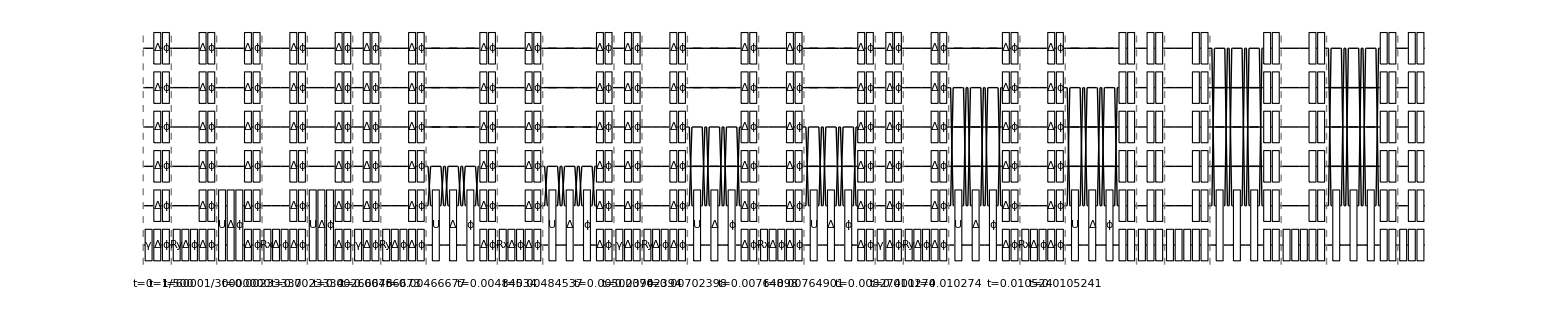

```mathematica
circInitOnDev=InsertCircuitNoise[Serialize@circInit,NVCenterDelft[],ReplaceAliases->True];
DrawCircuit[%,6]
```

```mathematica
ApplyCircuit[CloneQureg[ρ2,ρ],ExtractCircuit[circInitOnDev]];
CalcFidelity[ρ2,InitZeroState@ψ]
```

0.932583

```mathematica
DestroyAllQuregs[]
```

## Measurements

Measurements in the computational basis. Compare 4k shots of measurement to the fidelity set in the device

```mathematica
nshots=1000;
{ρ,ρinit}=CreateDensityQuregs[6,2];
```

#### On the electron spin

```mathematica
outputs=Flatten@Table[ApplyCircuit[InitZeroState@ρ,ExtractCircuit@InsertCircuitNoise[{Subscript[M, 0]},NVCenterDelft[],ReplaceAliases->True]]
,{nshots}];
Print["correct outputs(0):"<>ToString[nshots-Total@outputs], "\nflipped outputs(1):"<>ToString[Total@outputs],"\nfidelity:"<>ToString[N[1-Total@outputs/nshots]*100]]
```

correct outputs(0):955
flipped outputs(1):45
fidelity:95.5

```mathematica
OptionValue[NVCenterDelft,FidMeas]
```

0.946

#### Measurement on the nuclear spins

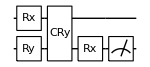

```mathematica
DrawCircuit[{Subscript[measZ, 1]}]
```

```mathematica
nshots=1000;
outputs=Flatten@Table[
ApplyCircuit[InitZeroState@ρ,ExtractCircuit@InsertCircuitNoise[{Subscript[measZ, 1]},NVCenterDelft[],ReplaceAliases->True]],{nshots}];
Print["correct outputs(0):"<>ToString[nshots-Total@outputs], "\nflipped outputs(1):"<>ToString[Total@outputs],"\nfidelity:"<>ToString[N[1-Total[outputs]/nshots]*100]]
```

correct outputs(0):940
flipped outputs(1):60
fidelity:94.

## BCS simulation

```mathematica
(* non-iteracting harmonic oscillator-type energy levels *)
ϵ=ω(#+0.5)&/@Range[0,4];
(* time-dependent coupling function *)
coupling[t_,g0_,gc_]:=ExpandAll[
(ArcTan[(t-t1)J/(ℏ Γ)]+π/2)(ArcTan[(t2-t)J/(ℏ Γ)]+π/2)(gc-g0)/π^2+g0
]
```

```mathematica
constants={
(* time start to quench and reverse. J is an arbitrary energy unit *)
t1->9 ℏ/J,
t2->18 ℏ/J,
(* initial coupling constant*)
Γ->0.1,
(* frequency *)
ω->5J/3
}
```

{t1→(9 ℏ)/J,t2→(18 ℏ)/J,Γ→0.1,ω→(5 J)/3}

```mathematica
(* mean-field eigenvalues *)
Ej[ϵ_,Δ_]:=Sqrt[ϵ^2+Abs[Δ]^2]
(* superconducting gap *)
(*2/g=∑_k 1/Subscript[E, k] tanh[Subscript[E, k]/(2 Subscript[k, b] Temp)]*)
(* since we consider temperature Temp=0, tanh(∞)=1 *)
(* Superconducting gaps*)
Δ0=J;
Δc=2J;
```

```mathematica
g0=2 /Total[1/Ej[ϵ,Δ0]];
gc=2/ Total[1/Ej[ϵ,Δc]];
```

The time-dependent gap Δ is controlled through g(t)

```mathematica
dense=0.1;
sparse=0.2;
τs=DeleteDuplicates@Join[Range[0,7,sparse],Range[7,21,dense],Range[21,27,sparse]];
```

```mathematica
Length@τs
```

206

```mathematica
(* the timesteps *)
δτ=Table[τs[[i]]-τs[[i-1]],{i,2,Length@τs}];
PrependTo[δτ,0];
(*sanity check*)
And@@Table[τs[[i]]==Total[δτ[[#]]&/@Range[i]],{i,Length@τs}]
```

True

```mathematica
(*τ=t J/ℏ*)
```

```mathematica
gvals=Simplify[(coupling[#*ℏ/Δ0,g0,gc]/Δ0&/@τs)//.constants,J>0];
```

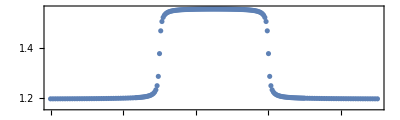

```mathematica
ListPlot[Transpose@{τs,gvals},PlotRange->{1.16,1.56},Joined->False,AspectRatio->0.3,Frame->True,FrameTicks->{{Range[1,1.55,0.05],None},{Range[0,27,3],None}}]
```

First part: Gaudin Hamiltonian

```mathematica
Hgaudin[q_,n_,ϵ_,g_]:=Total@Table[({Subscript[X, q],Subscript[Y, q],Subscript[Z, q]}.{Subscript[X, j],Subscript[Y, j],Subscript[Z, j]})/(2(ϵ[[q+1]]-ϵ[[j+1]])), {j,Complement[Range[0,n-1],{q}]}]+Subscript[Z, q]/g
```

```mathematica
(* Return the unitary of gaudin hamiltonian using MatrixExp *)
Ugaudin[n_,ϵ_,δt_,τ_]:=Module[{exp,g},
g=coupling[τ*ℏ/Δ0,g0,gc];
Table[
exp=ExpandAll@Simplify[(g*ϵ[[q+1]]*Hgaudin[q,n,ϵ,g]/ℏ)/.constants,J>0];
Subscript[U, Sequence@@Range[0,n-1]][MatrixExp[I*δt*CalcPauliStringMatrix[ExpandAll[(exp*ℏ/Δ0) /. constants]]]]
,{q,0,n-1}]
]
```

```mathematica
(* Return the trotterized gaudin hamiltonian *)
Tgaudin[n_,ϵ_,δt_,τ_]:=Module[{exp,g},
g=coupling[τ*ℏ/Δ0,g0,gc];
Table[
exp=ExpandAll@Simplify[(g*ϵ[[q+1]]*Hgaudin[q,n,ϵ,g]/ℏ)/.constants,J>0];

Subscript[U, Sequence@@Range[0,n-1]][MatrixExp[I*δt*CalcPauliStringMatrix[ExpandAll[(exp*ℏ/Δ0) /. constants]]]]
,{q,0,n-1}]
]
```

Second part: Ising Hamiltonian

```mathematica
(* Return the unitary of ising hamiltonian using MatrixExp *)
Uising[δt_,τ_,n_]:=Module[{g=coupling[τ*ℏ/Δ0,g0,gc],exp},
exp=Flatten@Table[If[j!=k,Simplify[( g/(Δ0*4) If[And[j<n-1,k<n-1],Subscript[Z, j] Subscript[Z, k] Subscript[Id, n-1],Subscript[Z, j] Subscript[Z, k]])/.constants,J>0],{}],
{j,0,n-1},{k,0,n-1}];
Subscript[U, Sequence@@Range[0,n-1]][MatrixExp[-ⅈ δt CalcPauliStringMatrix[#]]]&/@exp
]
```

Third part: single qubits Hamiltonian

```mathematica
(* Return the unitary of single spin hamiltonian. The same with circuit. *)
Usingle[δt_,τ_,n_]:=Table[Subscript[Rz, j][Simplify[(δt/Δ0 coupling[τ*ℏ/Δ0,g0,gc])/.constants,J>0] ],{j,0,n-1}]
```

The analytic values

```mathematica
(*mean field-eigenvalues*)
ej=Simplify[Ej[ϵ,Δ0]/.constants,J>0]
(* |Subscript[v, j]|^2, |Subscript[u, j]|^2 *)
ujs=Simplify[0.5(1+ϵ/ej)/.constants,J>0]
vjs=Simplify[0.5(1-ϵ/ej)/.constants,J>0]
```

{1.30171 J,2.69258 J,4.28499 J,5.91843 J,7.56637 J}

{0.820092,0.964238,0.986194,0.992811,0.995614}

{0.179908,0.0357617,0.0138063,0.00718887,0.00438605}

```mathematica
(*  
Subscript[u, j] 0-Subscript[v, j] 1;
Ry[θ]0=Cos[θ/2]0-Sin[θ/2]1 
 *)
θinit=2*ArcCos@Sqrt@ujs
(* double check *)
2*ArcSin@Sqrt@vjs
```

{0.876058,0.380506,0.235545,0.169778,0.132552}

{0.876058,0.380506,0.235545,0.169778,0.132552}

Result 1 : Calculate Rmf using MatrixExp function

```mathematica
DestroyAllQuregs[]
{ψ,ψinit}=CreateQuregs[5,2];
```

```mathematica
(* BCS as init state *)
ApplyCircuit[InitZeroState@ψ,Table[Subscript[Ry, j-1][θinit[[j]]],{j,5}]];
CloneQureg[ψinit,ψ];
(* Rmf(τ)*)
τ=0;
rmf=Table[
bcscirc=Flatten@{Ugaudin[5,ϵ,δ,τ],Uising[δ,τ,5],Usingle[δ,τ,5]};
ApplyCircuit[ψ,bcscirc];
out={τ,CalcFidelity[ψ,ψinit]};
τ+=δ;
out
,{δ,δτ}];
```

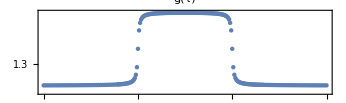

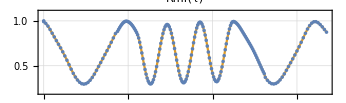

```mathematica
ListPlot[Transpose@{τs,gvals},PlotRange->{1.16,1.56},Joined->False,AspectRatio->0.3,Frame->True,FrameTicks->{{Range[1,1.55,0.05],None},{Range[0,27,3],None}},PlotLabel->"g(τ)"]
ListPlot[{rmf,rmf},PlotRange->{0.2,1.1},Joined->{False,True},PlotTheme->"Detailed",AspectRatio->0.3,PlotLabel->"Rmf(τ)"]
```